```mathematica
Eigenvalues[{{0,1},{2Sqrt[μ],0}}]
Eigenvectors[{{0,1},{2Sqrt[μ],0}}]
```

{-√2 μ^(1/4),√2 μ^(1/4)}

{{-1/(√2 μ^(1/4)),1},{1/(√2 μ^(1/4)),1}}

```mathematica
Eigenvalues[{{0,1},{-2Sqrt[μ],0}}]
Eigenvectors[{{0,1},{-2Sqrt[μ],0}}]
```

{-ⅈ √2 μ^(1/4),ⅈ √2 μ^(1/4)}

{{ⅈ/(√2 μ^(1/4)),1},{-ⅈ/(√2 μ^(1/4)),1}}

```mathematica
eigvec= Eigenvalues[{{0,0,1,0},{0,0,0,1},{2Sqrt[μ] - ϵ,ϵ,0,0},{ϵ,-(ω^2+ϵ),0,0}}];
eigvec/. μ -> 0.1 /. ϵ -> 0.1 /. ω -> 1.0
```

{0.-1.05171 ⅈ,0.+1.05171 ⅈ,-0.733865,0.733865}

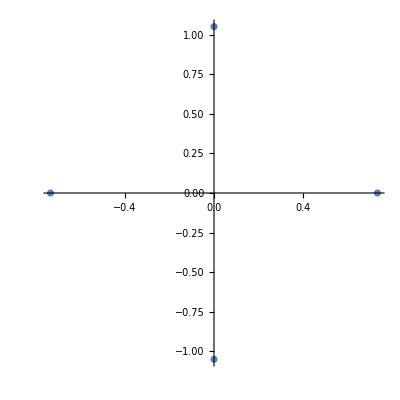

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@{0.-1.0517142793469199 ⅈ,0.+1.0517142793469199 ⅈ,-0.7338654218696279,0.7338654218696279},AspectRatio->1]
```

```mathematica
{-(√(-2 ϵ+2 √μ-ω^2-√(4 ϵ^2+4 μ+4 √μ ω^2+ω^4)))/(√2),(√(-2 ϵ+2 √μ-ω^2-√(4 ϵ^2+4 μ+4 √μ ω^2+ω^4)))/(√2),-√(-ϵ+√μ-ω^2/2+1/2 √(4 ϵ^2+4 μ+4 √μ ω^2+ω^4)),√(-ϵ+√μ-ω^2/2+1/2 √(4 ϵ^2+4 μ+4 √μ ω^2+ω^4))}
```

{-(√(-2 ϵ+2 √μ-ω^2-√(4 ϵ^2+4 μ+4 √μ ω^2+ω^4)))/(√2),(√(-2 ϵ+2 √μ-ω^2-√(4 ϵ^2+4 μ+4 √μ ω^2+ω^4)))/(√2),-√(-ϵ+√μ-ω^2/2+1/2 √(4 ϵ^2+4 μ+4 √μ ω^2+ω^4)),√(-ϵ+√μ-ω^2/2+1/2 √(4 ϵ^2+4 μ+4 √μ ω^2+ω^4))}

```mathematica
eigvec = Simplify[Eigenvectors[{{0,0,1,0},{0,0,0,1},{2Sqrt[μ] - ϵ,ϵ,0,0},{ϵ,-(ω^2+ϵ),0,0}}]]
eigvec/. μ -> 0.1 /. ϵ -> 0.1 /. ω -> 1.0
```

{{(-2 √μ-ω^2+√(4 ϵ^2+(2 √μ+ω^2)^2))/(√2 ϵ √(-2 ϵ+2 √μ-ω^2-√(4 ϵ^2+(2 √μ+ω^2)^2))),-(√2)/(√(-2 ϵ+2 √μ-ω^2-√(4 ϵ^2+(2 √μ+ω^2)^2))),(-2 ϵ^2+ϵ (2 √μ+ω^2-√(4 ϵ^2+(2 √μ+ω^2)^2))-2 √μ (2 √μ+ω^2-√(4 ϵ^2+(2 √μ+ω^2)^2)))/(ϵ (2 ϵ-2 √μ+ω^2+√(4 ϵ^2+(2 √μ+ω^2)^2))),1},{(2 √μ+ω^2-√(4 ϵ^2+(2 √μ+ω^2)^2))/(√2 ϵ √(-2 ϵ+2 √μ-ω^2-√(4 ϵ^2+(2 √μ+ω^2)^2))),(√2)/(√(-2 ϵ+2 √μ-ω^2-√(4 ϵ^2+(2 √μ+ω^2)^2))),(-2 ϵ^2+ϵ (2 √μ+ω^2-√(4 ϵ^2+(2 √μ+ω^2)^2))-2 √μ (2 √μ+ω^2-√(4 ϵ^2+(2 √μ+ω^2)^2)))/(ϵ (2 ϵ-2 √μ+ω^2+√(4 ϵ^2+(2 √μ+ω^2)^2))),1},{-(2 √μ+ω^2+√(4 ϵ^2+(2 √μ+ω^2)^2))/(√2 ϵ √(-2 ϵ+2 √μ-ω^2+√(4 ϵ^2+(2 √μ+ω^2)^2))),-(√2)/(√(-2 ϵ+2 √μ-ω^2+√(4 ϵ^2+(2 √μ+ω^2)^2))),(-2 ϵ^2+ϵ (2 √μ+ω^2+√(4 ϵ^2+(2 √μ+ω^2)^2))-2 √μ (2 √μ+ω^2+√(4 ϵ^2+(2 √μ+ω^2)^2)))/(ϵ (2 ϵ-2 √μ+ω^2-√(4 ϵ^2+(2 √μ+ω^2)^2))),1},{(2 √μ+ω^2+√(4 ϵ^2+(2 √μ+ω^2)^2))/(√2 ϵ √(-2 ϵ+2 √μ-ω^2+√(4 ϵ^2+(2 √μ+ω^2)^2))),(√2)/(√(-2 ϵ+2 √μ-ω^2+√(4 ϵ^2+(2 √μ+ω^2)^2))),(-2 ϵ^2+ϵ (2 √μ+ω^2+√(4 ϵ^2+(2 √μ+ω^2)^2))-2 √μ (2 √μ+ω^2+√(4 ϵ^2+(2 √μ+ω^2)^2)))/(ϵ (2 ϵ-2 √μ+ω^2-√(4 ϵ^2+(2 √μ+ω^2)^2))),1}}

```mathematica
{{0.-0.05802835905205023 ⅈ,0.+0.9508285849470136 ⅈ,-0.06102925382211011,1},{0.+0.05802835905205023 ⅈ,0.-0.9508285849470136 ⅈ,-0.06102925382211011,1},{-22.327778480711395,-1.3626476601831925,16.38558457415887,1},{22.327778480711395,1.3626476601831925,16.38558457415887,1}}
```

{{0.-0.0580284 ⅈ,0.+0.950829 ⅈ,-0.0610293,1},{0.+0.0580284 ⅈ,0.-0.950829 ⅈ,-0.0610293,1},{-22.3278,-1.36265,16.3856,1},{22.3278,1.36265,16.3856,1}}